```mathematica
ClearAll["Global`*"];
```

```mathematica
(*Symbolic parameters*)
f[R_,c_,r_,k_,α_,η_]:=r R (1-R/k)-(α R c)/(1+α η R)
g[R_,c_,ε_,β_,α_,η_]:=ε (α R c)/(1+α η R)-β c
```

```mathematica
(*Solve f=0,g=0*)
sol=Solve[{f[R,c,r,k,α,η]==0,g[R,c,ε,β,α,η]==0},{R,c}][[3]] (*Trivial solutions {R->0,c->0} and {R->k,c->0} are not of interest*)
RstarSol=R/.sol[[1]]
cstarSol=c/.sol[[2]]
```

{R→β/(α (ε-β η)),c→(r ε (-β+k α ε-k α β η))/(k α^2 (ε-β η)^2)}

β/(α (ε-β η))

(r ε (-β+k α ε-k α β η))/(k α^2 (ε-β η)^2)

```mathematica
Jacobi=D[{f[R,c,r,k,α,η],g[R,c,ε,β,α,η]},{{R,c}}]
```

{{-(r R)/k+r (1-R/k)+(c R α^2 η)/(1+R α η)^2-(c α)/(1+R α η),-(R α)/(1+R α η)},{-(c R α^2 ε η)/(1+R α η)^2+(c α ε)/(1+R α η),-β+(R α ε)/(1+R α η)}}

```mathematica
JacobianAtEq=Jacobi/.{R->RstarSol,c->cstarSol}
```

{{-(r β)/(k α (ε-β η))+r (1-β/(k α (ε-β η)))+(r β ε η (-β+k α ε-k α β η))/(k α (ε-β η)^3 (1+(β η)/(ε-β η))^2)-(r ε (-β+k α ε-k α β η))/(k α (ε-β η)^2 (1+(β η)/(ε-β η))),-β/((ε-β η) (1+(β η)/(ε-β η)))},{-(r β ε^2 η (-β+k α ε-k α β η))/(k α (ε-β η)^3 (1+(β η)/(ε-β η))^2)+(r ε^2 (-β+k α ε-k α β η))/(k α (ε-β η)^2 (1+(β η)/(ε-β η))),-β+(β ε)/((ε-β η) (1+(β η)/(ε-β η)))}}

```mathematica
tr=Tr[JacobianAtEq]//Simplify
det=Det[JacobianAtEq]//Simplify
```

-(r β (ε-k α ε η+β η (1+k α η)))/(k α ε (ε-β η))

-(r β (β-k α ε+k α β η))/(k α ε)

```mathematica
(*Stable equilibrium:trace<0 and determinant>0*)
stableConditions=Reduce[{tr<0,det>0,RstarSol>0,cstarSol>0},{β,η},Reals]
```

(ε<0&&((α<0&&r>0&&k>0&&β<0&&(-β+k α ε)/(k α β)<η<(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(α>0&&((r<0&&((k<0&&β>0&&η<ε/β)||(k>0&&β>0&&η<(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))))||(r>0&&k>0&&β>0&&(-β+k α ε)/(k α β)<η<ε/β)))))||(ε>0&&((α<0&&((r<0&&((k<0&&β<0&&ε/β<η<(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(k>0&&3 k α ε+2 √2 √(k^2 α^2 ε^2)<β<0&&(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))<η<(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))))||(r>0&&k>0&&((β<3 k α ε-2 √2 √(k^2 α^2 ε^2)&&(ε/β<η<(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))<η<(-β+k α ε)/(k α β)))||(β==3 k α ε-2 √2 √(k^2 α^2 ε^2)&&(ε/β<η<(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))<η<(-β+k α ε)/(k α β)))||(3 k α ε-2 √2 √(k^2 α^2 ε^2)<β<0&&ε/β<η<(-β+k α ε)/(k α β))))))||(α>0&&((r<0&&k>0&&β>3 k α ε+2 √2 √(k^2 α^2 ε^2)&&(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))<η<(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(r>0&&((k<0&&β>0&&η<(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(k>0&&((0<β<3 k α ε-2 √2 √(k^2 α^2 ε^2)&&(η<(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))<η<(-β+k α ε)/(k α β)))||(β==3 k α ε-2 √2 √(k^2 α^2 ε^2)&&(η<(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))<η<(-β+k α ε)/(k α β)))||(β>3 k α ε-2 √2 √(k^2 α^2 ε^2)&&η<(-β+k α ε)/(k α β))))))))))

```mathematica
hopfConditions=Reduce[{tr==0,det>0,RstarSol>0,cstarSol>0},{β,η},Reals]
```

(k<0&&((r<0&&α<0&&ε>0&&β<0&&η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(r>0&&α>0&&ε>0&&β>0&&η==(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))))||(k>0&&((r<0&&((α<0&&ε>0&&((β==3 k α ε+2 √2 √(k^2 α^2 ε^2)&&η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(3 k α ε+2 √2 √(k^2 α^2 ε^2)<β<0&&(η==(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))))))||(α>0&&((ε<0&&β>0&&η==(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(ε>0&&((β==3 k α ε+2 √2 √(k^2 α^2 ε^2)&&η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(β>3 k α ε+2 √2 √(k^2 α^2 ε^2)&&(η==(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))))))))))||(r>0&&((α<0&&((ε<0&&β<0&&η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))||(ε>0&&((β<3 k α ε-2 √2 √(k^2 α^2 ε^2)&&(η==(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))))||(β==3 k α ε-2 √2 √(k^2 α^2 ε^2)&&η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))))))||(α>0&&ε>0&&((0<β<3 k α ε-2 √2 √(k^2 α^2 ε^2)&&(η==(-β+k α ε)/(2 k α β)-1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))||η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2))))||(β==3 k α ε-2 √2 √(k^2 α^2 ε^2)&&η==(-β+k α ε)/(2 k α β)+1/2 √((β^2-6 k α β ε+k^2 α^2 ε^2)/(k^2 α^2 β^2)))))))))

```mathematica
paramVals={r->0.3,k->1,α->2,ε->1};
ηval=0.5;
βval=0.25;
RstarNum[η_?NumericQ,β_?NumericQ]:=RstarSol/.paramVals
cstarNum[η_?NumericQ,β_?NumericQ]:=cstarSol/.paramVals
{RstarNum[η=ηval,β=βval],cstarNum[η=ηval,β=βval]}
```

{0.142857,0.146939}

```mathematica
trNum[η_?NumericQ,β_?NumericQ]:=tr/.paramVals
detNum[η_?NumericQ,β_?NumericQ]:=det/.paramVals
{trNum[η=ηval,β=βval],detNum[η=ηval,β=βval]}
```

{-0.0107143,0.05625}

```mathematica
validRegion[η_?NumericQ,β_?NumericQ]:=(RstarNum[η,β]>0&&cstarNum[η,β]>0)
stable[η_?NumericQ,β_?NumericQ]:=validRegion[η,β]&&trNum[η,β]<0&&detNum[η,β]>0
dampedOsc[η_?NumericQ,β_?NumericQ]:=stable[η,β]&&(trNum[η,β]^2-4 detNum[η,β]<0)
nonOsc[η_?NumericQ,β_?NumericQ]:=stable[η,β]&&(trNum[η,β]^2-4 detNum[η,β]>=0);
hopf[η_?NumericQ,β_?NumericQ]:=validRegion[η,β]&&trNum[η,β]>=0&&detNum[η,β]>0;
nonCoexist[η_?NumericQ,β_?NumericQ]:=!validRegion[η,β];
```

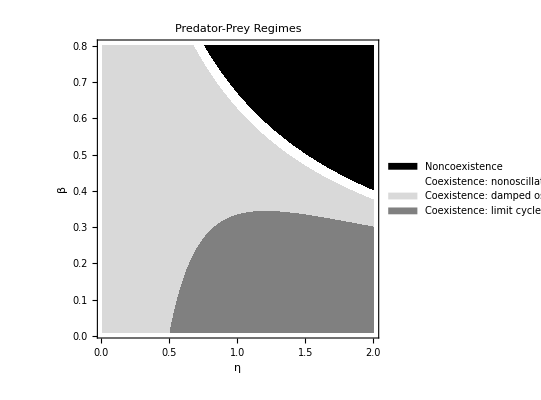

```mathematica
Show[Legended[RegionPlot[nonCoexist[η,β],{η,0.01,2},{β,0.01,0.8},PlotPoints->100,PlotStyle->Black,BoundaryStyle->None],SwatchLegend[{Black},{"Noncoexistence"}]],Legended[RegionPlot[nonOsc[η,β],{η,0.01,2},{β,0.01,0.8},PlotPoints->100,PlotStyle->White,BoundaryStyle->None],SwatchLegend[{White},{"Coexistence: nonoscillatory"}]],Legended[RegionPlot[dampedOsc[η,β],{η,0.01,2},{β,0.01,0.8},PlotPoints->100,PlotStyle->LightGray,BoundaryStyle->None],SwatchLegend[{LightGray},{"Coexistence: damped oscillations"}]],Legended[RegionPlot[hopf[η,β],{η,0.01,2},{β,0.01,0.8},PlotPoints->100,PlotStyle->Gray,BoundaryStyle->None],SwatchLegend[{Gray},{"Coexistence: limit cycles"}]],FrameLabel->{"η","β"},PlotLabel->"Predator-Prey Regimes",PlotLegends->Placed[SwatchLegend[{Black,White,LightGray,Gray},{"Noncoexistence","Coexistence: nonoscillatory","Coexistence: damped oscillations", "Coexistence: limit cycles"}],Right]]
```